# Delft’s Silicon device

reference: https://arxiv.org/abs/2202.09252
scientific contributors: Fernando, Simon

Recent Silicon device inspired by the Delft

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

Connectivity of this device

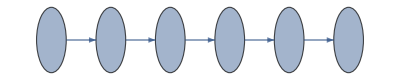

```mathematica
Graph[Range[0,5],Table[j->j+1,{j,0,4}],VertexLabels->Placed[Automatic,Center],VertexSize->.5]
```

Set the default configuration of the device

```mathematica
Options[SiliconDelft]={
qubitsNum->6,
(*average of T1*)
T1->100,
(* T2* *)
T2s-><|0->3,1-> 2.5,2-> 3.7,3-> 3.7,4-> 5.9,5-> 5.1|>,
(* T2 obtained by echo RX[π/2]-τ-RX[π]-τ-RX[π/2], where τ=1μs *)
T2-><|0->14,1-> 21.1,2-> 40.1,3-> 37.2,4-> 44.7,5-> 26.7|>,
(* If true, then the noise model uses T2s otherwise T2 *)
DDActive->True,
(* EDIT: Qubit frequency of each qubit in MHz *)
QubitFreq-><|0->15.62*10^3,1-> 15.88*10^3,2-> 16.3*10^3,3-> 16.1*10^3,4-> 15.9*10^3,5-> 15.69*10^3|>,
(*rabi frequencies on single rotations *)
RabiFreq-><|0->8,1->5,2->5,3->5,4->5,5->5|>,
(* Set the noise form of off-resonant Rabi oscillation. This takes RabiFreq information to produce the noise.*)
OffResonantRabi->True,

(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->True,

(* Fidelities of X- and Y- rotations by random benchmarking *)
FidSingleXY-><|0->0.9977,1-> 0.9987,2-> 0.9996,3-> 0.9988,4-> 0.9991,5-> 0.9989|>,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingleXY->{0,1},
(*  The rabi Frequency (MHz) and fidelities of controlled-Z, C[Z], nearest-neighbors, where the control qubits are the lower one. Keys are the control qubits *)
FreqCZ-><|0->12.1,1-> 11.1,2-> 6.6,3-> 9.8,4-> 5.4|>,
FidCZ-><|0->0.8961173996 ,1->0.903347176,2-> 0.8837068241 ,3->0.9582985365,4-> 0.9426960894|>,
(* Error fraction/ratio {depolarising, dephasing} of controled-Rz rotation *)
EFCZ->{0.2,0.8},
(* Crosstalks error (C-Rz[ex])on the passive qubits when applying CZ gates;square matrix with dims nqubit-2
*)
ExchangeRotOn->{{0,0.023, 0.018 ,0.03, 0.04},{0.05 ,0,0.03, 0.03, 0.04},{0.05, 0.03 ,0,0.07, 0.042},{0.038 ,0.03 ,0.031,0 ,0.25},{0.033, 0.03 ,0.02, 0.03,0}},
(* Crosstalks error (C-Rz[ex])on the passive qubits when no CZ gates applied *)
ExchangeRotOff-><|0->0.039,1-> 0.015 ,2->0.03 ,3->0.02,4-> 0.028|>,

(* Single readout fidelity and duration of the edge qubits, ie 01 and 56 *)
FidRead->0.99,
DurRead->10,
RepeatRead->2
};
```

Native gates: Rx_j[θ],  Ry_j[θ], C_i[Z_(i+1)],Meas, Init,  Wait_-1[Δt]

## Tests

```mathematica
ψ=CreateQureg[6];
ρ=CreateDensityQureg[6];
```

Remarks:
the time unit is μs

### Passive noise

The passive noise when no gates are applied.
The noise forms:
1) Cross-talk C_i[Rz_(i+1)(Δt)]  from input ExchangeRotOff, which is exchange rotation when no C[Z] gate is applied. 
2) Standard dephasing from T2 or T2* input and depolarising from T1 inputs.
3) If dynamical decoupling is active, DDActive->True, then T2 information is used, otherwise T2s information used. 

The standard passivenoise (2) can be eliminated by setting StdPassiveNoise -> False. The Cross-talk (1) can be set off by setting ExchangeRotOff->False

{{0,{C_0[Rz_1[0.124141]],Deph_0[0.255229],Depol_0[0.0713719]},{C_0[Rz_1[0]],Deph_0[0],Depol_0[0],C_1[Rz_2[0.0477465]],Deph_1[0.188726],Depol_1[0.0713719],C_2[Rz_3[0.095493]],Deph_2[0.110357],Depol_2[0.0713719],C_3[Rz_4[0.063662]],Deph_3[0.117859],Depol_3[0.0713719],C_4[Rz_5[0.0891268]],Deph_4[0.100228],Depol_4[0.0713719],Deph_5[0.156194],Depol_5[0.0713719]}}}

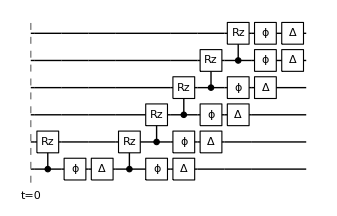

```mathematica
circ={Subscript[Wait, 0][10]};
InsertCircuitNoise[{#}&/@circ,SiliconDelft[StdPassiveNoise->True,DDActive->True]]//Chop
DrawCircuit@%
```

### Single qubit gates

Single qubit gates: x- and y- rotations have the same error 
The noise forms:
1) Off-resonant Rabi Oscillation. This takes RabiFreq input and applied when OffResonantRabi->True.
2) Standard Dephasing and Depolarising noise. This takes FidSingleXY and EFSingleXY inputs to estimate the error parameters. Set EFSingleXY->{0,0} to set this off.

remove Rz

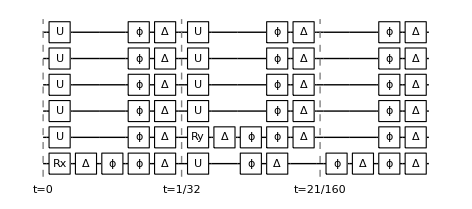

```mathematica
circ={Subscript[Rx, 0][π/2],Subscript[Ry, 1][π],Subscript[Wait, 0][1]};
InsertCircuitNoise[{#}&/@circ,SiliconDelft[StdPassiveNoise->True,OffResonantRabi->True,ExchangeRotOff->False]]//Chop;
DrawCircuit[%]
```

Controlled-Z

The noise forms:
1) Standard 2-qubits dephasing and depolarising noise. This takes information FidCZ (fidelities) and EFCZ (error fraction). Set it off by EFCZ->{0,0}
2) Exchange rotation when C-Z is on. Takes information ExchangeRotOn. Set ExchangeRotOn -> False to set it off.

How to integrate this in general scheme?

{{0,{C_0[Z_1],Depol_(0,1)[0],Deph_(0,1)[0],C_1[Rz_2[0.023]],C_2[Rz_3[0.018]],C_3[Rz_4[0.03]],C_4[Rz_5[0.04]]},{Deph_0[0.],Depol_0[0.],Deph_1[0.],Depol_1[0.],Deph_2[0.000514975],Depol_2[0.000309853],Deph_3[0.000555099],Depol_3[0.000309853],Deph_4[0.000462005],Depol_4[0.000309853],Deph_5[0.000773228],Depol_5[0.000309853]}}}

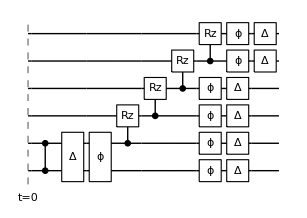

```mathematica
InsertCircuitNoise[{Subscript[C, 0][Subscript[Z, 1]]},SiliconDelft[StdPassiveNoise->True,ExchangeRotOff->False,EFCZ->{0,0}]]
DrawCircuit[%]
```

## Reproducing results from the paper

Initialisation is obtained by 2 readouts and a partial swap with single qubit errors
The qubits are initialised to state 100 ... 001

### Initialisation fidelity goal: 0.95 (quoted value)

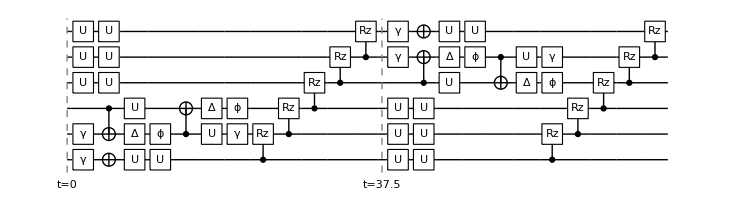

0.949981

```mathematica
(* initialise the qubits to mixed state *)
SetQuregMatrix[ρ,RandomMixState[6]];
noisycirc=InsertCircuitNoise[SerializeCircuit@{Subscript[Init, 0,1,2],Subscript[Init, 3,4,5]},SiliconDelft[StdPassiveNoise->False]];
ApplyCircuit[ρ,ExtractCircuit@noisycirc];
DrawCircuit@noisycirc
ApplyCircuit[InitZeroState@ψ,{Subscript[X, 0],Subscript[X, 5]}];
CalcFidelity[ρ,ψ]
```

### T_1 average with perfect measurement

```mathematica
ApplyCircuit[InitZeroState@ψ,{Subscript[X, 0],Subscript[X, 5]}];
```

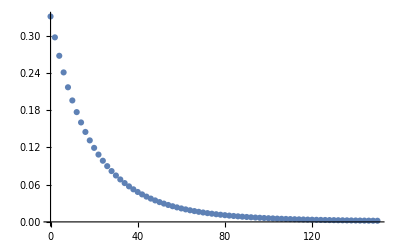

```mathematica
Table[
(* initialise the qubits to mixed state *)
SetQuregMatrix[ρ,RandomMixState[6]];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[SerializeCircuit@{Subscript[Init, 0,1,2],Subscript[Init, 3,4,5],Subscript[Wait, 0][t]},
SiliconDelft[DDActive->True,StdPassiveNoise->True]
]];
{t, CalcFidelity[ρ,ψ]^2}
,{t,Range[0,150,2]}];
ListPlot[%,PlotRange->All]
```

### Obtaining T_2 from T_2^* X90 - tau - X180 - tau - X90, tau = 1 us

Calculate the T2 of qubit 1

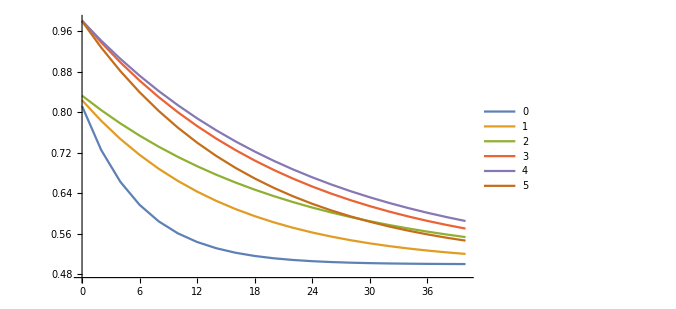

```mathematica
Table[
(* initialise the qubits to mixed state *)
SetQuregMatrix[ρ,RandomMixState[6]];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[SerializeCircuit@{Subscript[Init, 0,1,2],Subscript[Init, 3,4,5],Sequence@@Table[Subscript[Rx, q][π/2],{q,Range[0,5]}],Subscript[Wait, 0][t],Sequence@@(Subscript[Rx, #][π]&/@Range[0,5]),Subscript[Wait, 0][t],Sequence@@Table[Subscript[Rx, q][π/2],{q,Range[0,5]}]},SiliconDelft[DDActive->True,StdPassiveNoise->True,EFSingleXY->{1,0},OffResonantRabi->False]]];
Table[{t,CalcProbOfOutcome[ρ,q,If[Or[q===0,q===5],1,0]]},{q,Range[0,5]}]
,{t,Range[0,40,2]}];
ListPlot[%[[All,#]]&/@Range[6],PlotLegends->Range[0,5],Joined->True,ImageSize->500]
```

### Bell states

```mathematica
ψ2=CreateQureg[2];
ρ2=CreateDensityQureg[2];
```

```mathematica
bellcircρ=<|"01"->{Subscript[Rx, 0][π/2],Subscript[Rx, 1][-π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]},"12"->{Subscript[Rx, 1][π/2],Subscript[Rx, 2][π/2],Subscript[C, 1][Subscript[Z, 2]],Subscript[Rx, 2][π/2]},"23"->{Subscript[Rx, 2][π/2],Subscript[Rx, 3][π/2],Subscript[C, 2][Subscript[Z, 3]],Subscript[Rx, 3][π/2]},"34"->{Subscript[Rx, 3][π/2],Subscript[Rx, 4][π/2],Subscript[C, 3][Subscript[Z, 4]],Subscript[Rx, 4][π/2]},"45"->{Subscript[Rx, 4][π/2],Subscript[Rx, 5][-π/2],Subscript[C, 4][Subscript[Z, 5]],Subscript[Rx, 5][-π/2]}|>;
bellcircψ=<|"01"->{Subscript[X, 0],Subscript[Rx, 0][π/2],Subscript[Rx, 1][-π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]},"12"->{Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]},"23"->{Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]},"34"->{Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]},"45"->{Subscript[X, 1],Subscript[Rx, 0][π/2],Subscript[Rx, 1][-π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][-π/2]}|>;
```

```mathematica
bell[code_,dev_]:=Module[{init={},qubits,fid,plot},
qubits=ToExpression@StringSplit[code,""];
If[Length@Intersection[qubits,{0,1,2}]>0,AppendTo[init,Subscript[Init, 0,1,2]]];
If[Length@Intersection[qubits,{3,4,5}]>0,AppendTo[init,Subscript[Init, 3,4,5]]];

SetQuregMatrix[ρ,RandomMixState[6]];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[SerializeCircuit@Flatten@{init,bellcircρ[code]},dev]];
SetQuregMatrix[ρ2,PartialTrace[ρ,Sequence@@Complement[Range[0,5],qubits]]];
ApplyCircuit[InitZeroState@ψ2,bellcircψ[code]];
fid=CalcFidelity[ρ2,ψ2];
plot=PlotDensityMatrix[ρ2,ImageSize->200,BarSpacing->0];
{plot,"Fid"<>code<>"="<>ToString@fid}
]
```

-Graphics-

```mathematica
dev=SiliconDelft[StdPassiveNoise->False,OffResonantRabi->True];
Grid@Transpose[bell[#,dev]&/@ReplaceList[Sort@Range[0,5],{p___,a_,b_,q___}:>StringRiffle[{a,b},""]]]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
Fid01=0.860432 | Fid12=0.876666 | Fid23=0.848947 | Fid34=0.926904 | Fid45=0.91507

### 3 - qubits GHZ

```mathematica
ψ3=CreateQureg[3];
ρ3=CreateDensityQureg[3];
```

```mathematica
ghzcircρ=<|
"012"->{Subscript[Rx, 0][-π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][-π/2],Subscript[Rx, 2][π/2],Subscript[C, 1][Subscript[Z, 2]],Subscript[Rx, 2][-π/2]},"123"->{Subscript[Rx, 1][π/2],Subscript[Rx, 2][π/2],Subscript[C, 1][Subscript[Z, 2]],Subscript[Rx, 2][-π/2],Subscript[Rx, 3][π/2],Subscript[C, 2][Subscript[Z, 3]],Subscript[Rx, 3][-π/2]},
"234"->{Subscript[Rx, 2][π/2],Subscript[Rx, 3][π/2],Subscript[C, 2][Subscript[Z, 3]],Subscript[Rx, 3][-π/2],Subscript[Rx, 4][π/2],Subscript[C, 3][Subscript[Z, 4]],Subscript[Rx, 4][-π/2]},
"345"->{Subscript[Rx, 3][-π/2],Subscript[Rx, 4][π/2],Subscript[C, 3][Subscript[Z, 4]],Subscript[Rx, 4][π/2],Subscript[Rx, 5][-π/2],Subscript[C, 4][Subscript[Z, 5]],Subscript[Rx, 5][π/2]}
|>;
ghzcircψ=<|
"012"->Join[{Subscript[X, 0]},ghzcircρ["012"]],
"123"->{Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][-π/2],Subscript[Rx, 2][π/2],Subscript[C, 1][Subscript[Z, 2]],Subscript[Rx, 2][-π/2]},
"234"->{Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][-π/2],Subscript[Rx, 2][π/2],Subscript[C, 1][Subscript[Z, 2]],Subscript[Rx, 2][-π/2]},
"345"->{Subscript[X, 2],Subscript[Rx, 0][π/2],Subscript[Rx, 1][-π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2],Subscript[Rx, 2][π/2],Subscript[C, 1][Subscript[Z, 2]],Subscript[Rx, 2][π/2]}
|>;

ghz[code_,dev_]:=Module[{init={},qubits,fid,plot},
qubits=ToExpression@StringSplit[code,""];
If[Length@Intersection[qubits,{0,1,2}]>0,AppendTo[init,Subscript[Init, 0,1,2]]];
If[Length@Intersection[qubits,{3,4,5}]>0,AppendTo[init,Subscript[Init, 3,4,5]]];
SetQuregMatrix[ρ,RandomMixState[6]];
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[SerializeCircuit@Flatten@{init,ghzcircρ[code]},dev]];
SetQuregMatrix[ρ3,PartialTrace[ρ,Sequence@@Complement[Range[0,5],qubits]]];
ApplyCircuit[InitZeroState@ψ3,ghzcircψ[code]];
fid=CalcFidelity[ρ3,ψ3]*Times@@(OptionValue[SiliconDelft,FidSingleXY][#]&/@qubits);
plot=PlotDensityMatrix[ρ3,ImageSize->200,BarSpacing->0];
{plot,"Fidest"<>code<>"="<>ToString@fid}
]
```

-Graphics-

```mathematica
dev=SiliconDelft[StdPassiveNoise->False,OffResonantRabi->True];
Grid@Transpose[ghz[#,dev]&/@ReplaceList[Sort@Range[0,5],{p___,a_,b_,c_,q___}:>StringRiffle[{a,b,c},""]]]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
Fidest012=0.749981 | Fidest123=0.711374 | Fidest234=0.770984 | Fidest345=0.827118